# Project - Green Bonds

Green Bonds are debt instruments issued by governments, corporations, and other entities to finance projects that have environmental benefits . They are similar to traditional bonds in that they provide investors with a fixed income stream over a specified period of time . The difference is that the proceeds from green bonds are used to fund projects that have positive environmental impacts, such as renewable energy, energy efficiency, clean transportation, and sustainable water management . Green bonds can be used to finance both new and existing projects .

## Video: https://youtu.be/j0VlfqVXUQI

## Import the Truecost Dataset on green bonds

```mathematica
dataGB1= Import["https://github.com/Nelson-Ortiz/ML2/blob/8003fa3518236502064ec79fa72f6d4f45b1f405/ECOL_GreenBonds_20220825.csv?raw=true","Dataset",HeaderLines->1];
RandomSample[dataGB1,5]
Dimensions@dataGB1
dataGB1[1];
```

{781,86}

## Exploring data

```mathematica
Keys[dataGB1[1]];
```

## Size

What is the distribution for the Bond’s size?

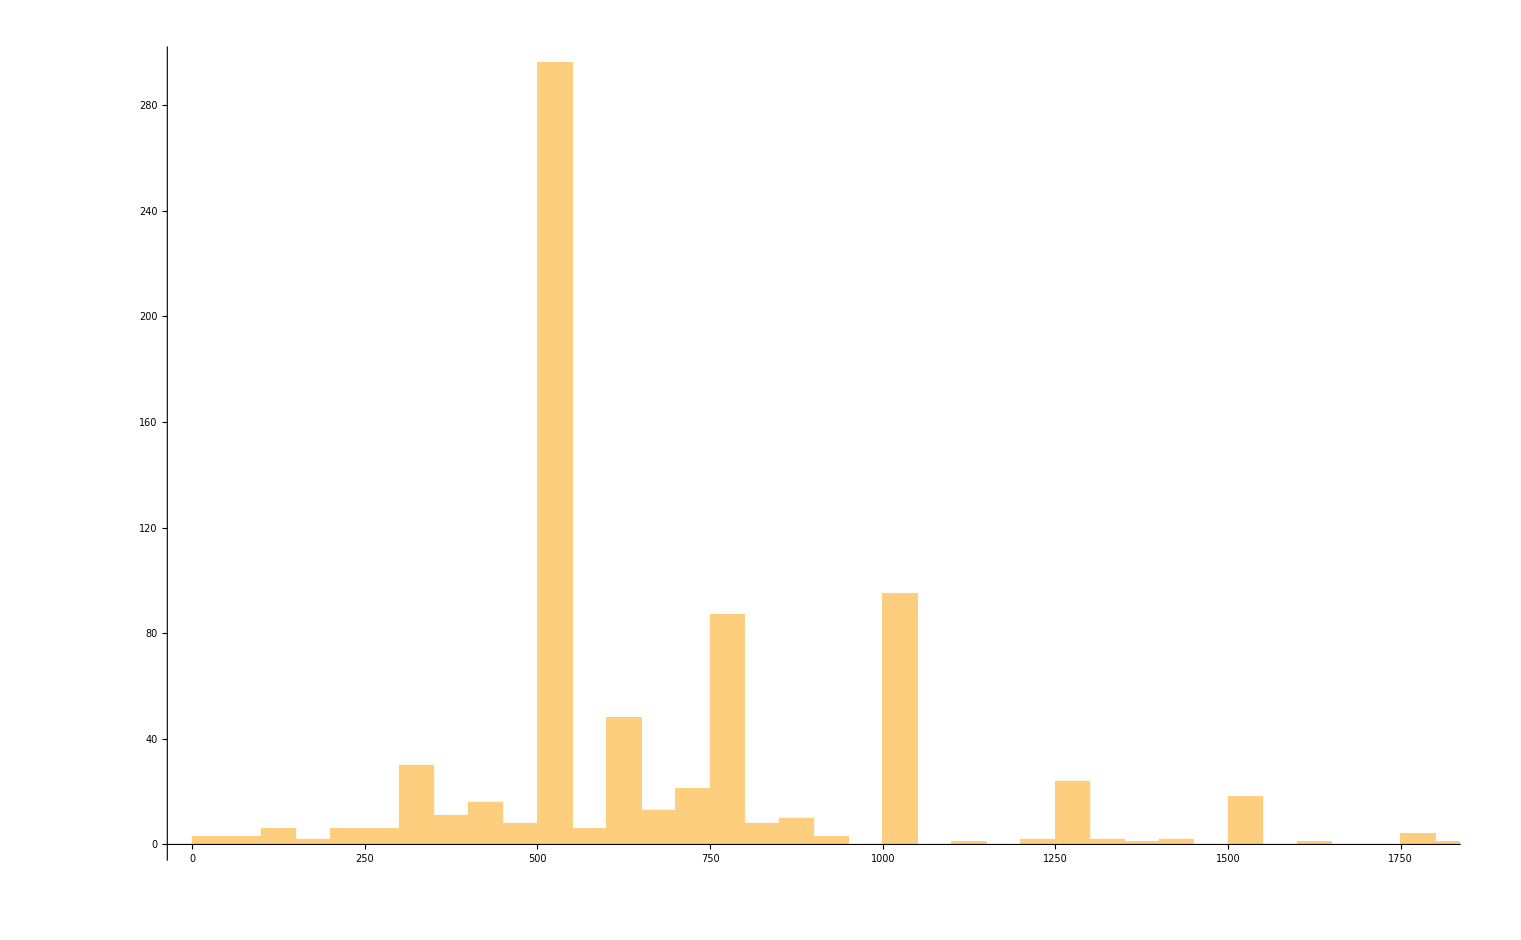

```mathematica
Histogram[dataGB1[All,"Nominal Amount"],{50}]
```

## Countries

Which countries issued the most green bonds?

```mathematica
GeoHistogram[dataGB1[All,{"Issuer Country of Origin"->(Interpreter["Country"][#]&)}][All,"Issuer Country of Origin"],"Country"]
```

-Graphics-

## Issuers

How many issuers are there ?  369

```mathematica
dataGB1[GroupBy["Issuer Name"]]
```

Dataset[<>]

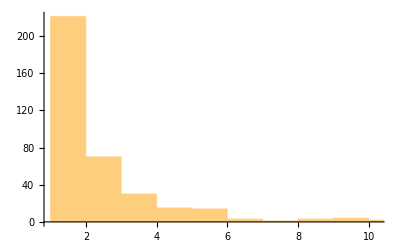

```mathematica
Histogram@(Length@dataGB1[GroupBy["Issuer Name"]][#]&/@Range[Length@dataGB1[GroupBy["Issuer Name"]]])
```

Most entities have only between 1-5 green bond reports in the dataset

```mathematica
listOfEntities=dataGB1[All,"Issuer Name"]//Normal//DeleteDuplicates[#]&;
countNum=Count[dataGB1[All,"Issuer Name"]//Normal,#]&/@listOfEntities;
```

```mathematica
numOfGBperCompany=AssociationThread[listOfEntities,countNum]//Dataset;
numOfGBperCompany=Sort[numOfGBperCompany,Greater]
```

## Classificator

## Add text column

```mathematica
sources=dataGB1[All,"Sources"]//Normal;
```

we extract once the text from the PDFs and then we store it on a local file for the next times

```mathematica
(*text=Import[#,"Plaintext"]&/@sources*)
text= Import["https://github.com/Nelson-Ortiz/ML2/blob/77b496d1cd237ecfbd746663ac576980f6cf2a36/texts.csv?raw=true"];
```

```mathematica
(*Export["texts.csv",text]*)
```

```mathematica
textAssoc=AssociationThread["Text"->#]&/@text;
dataGB2=Join[dataGB1//Normal,textAssoc,2]//Dataset;
(*dataGB2Clean=dataGB2[Select[!FailureQ[#Text]&]];*)  (*remove data points without text*)
dataGB2Clean=dataGB2[Select[!StringMatchQ[#Text,"$Failed"]&]];
dataGB2Clean=dataGB2Clean[All,Append[#,"TextSplit"->StringSplit[#Text]]&];(*add a column which transform Text into a list of words*)
dataGB2Clean=dataGB2Clean[All,Append[#,"TextSplitClean"->DeleteStopwords[#TextSplit]]&];  (*Delete the stop words from the text*)
dataGB2Clean=dataGB2Clean[Select[#TextSplit != {} &]];(* remove points with empty texts*)
```

```mathematica
{Dimensions@dataGB2,Dimensions@dataGB2Clean}
```

{{781,87},{395,89}}

## Create classificator

### Classificator CBI Category

#### Clean Data

Check the CBI Category

```mathematica
dataGB2Clean[All,"CBI Category"]//Normal//DeleteDuplicates
```

{Renewable Electricity and Heat Production,Buildings,Others Green,Transport,No sufficient information,Land Use and Marine Resources,Undisclosed/Not disbursed proceeds,Water,Transmission, distribution & storage,No Sufficient Information,ICT,Social,Proceeds that are Not Green,Insufficient information,Waste}

Then we merge {No sufficient information,No Sufficient Information,Insufficient information, Undisclosed/Not disbursed proceeds} into a single category “Insufficent Information”

```mathematica
listII={"No sufficient information","No Sufficient Information","Insufficient information","Undisclosed/Not disbursed proceeds"}
```

{No sufficient information,No Sufficient Information,Insufficient information,Undisclosed/Not disbursed proceeds}

```mathematica
dataCBI=dataGB2Clean[All,Append[#,"CBI Category Clean"->(If[ContainsAny[{#["CBI Category"]},listII],"Insufficent Information",#["CBI Category"]])]&];
```

```mathematica
dataCBI[All,{"CBI Category","CBI Category Clean"}];
```

#### Create training/test set

```mathematica
dataCBI[1]//Keys//Normal;
{nobs,ncol}=Dimensions[dataCBI[All,{"CBI Category Clean","TextSplit"}]]
{trainingset,testset}=TakeDrop[RandomSample[dataCBI[All,{"CBI Category Clean","TextSplit"}]],Round[nobs*0.8,1]];
```

{395,2}

#### Create classificator

ClassifierFunction[…]

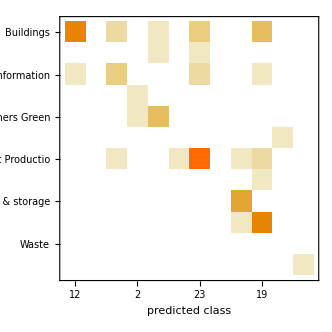
Classifier Measurements
Classifier method | Markov
Number of test examples | 79
Accuracy | (68.5.) %
Accuracy baseline | (28.5.) %
Mean cross entropy | 2200. ± 1700.
Single evaluation time | 27.2 ms/example
Batch evaluation speed | 16.8 examples/s
-Graphics- |

```mathematica
cCategory = Classify[trainingset-> "CBI Category Clean"]
cm =ClassifierMeasurements[cCategory,testset]
```

```mathematica
cm["Properties"];
```

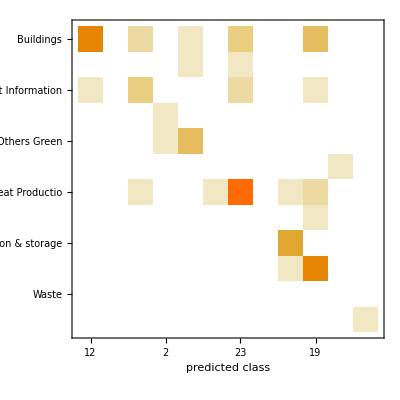

```mathematica
cm["ConfusionMatrixPlot"]//Show[#,ImageSize->Full]&
```

## Web Interface

```mathematica
classifierFunction[x_]:= cCategory[Association["TextSplit"->StringSplit[Import[x,"Plaintext"]]]]
```

```mathematica
dataGB1[6,"Sources"]
```

https://www.eib.org/attachments/fi/cab-statement-2016.pdf

```mathematica
cloudfunc= APIFunction[{"PDFName"->"String"},cCategory[Association["TextSplit"->StringSplit[Import[#PDFName,"Plaintext"]]],"TopProbabilities"]&]
```

APIFunction[{PDFName→String},cCategory[Association[TextSplit→StringSplit[Import[#PDFName,Plaintext]]],TopProbabilities]&]

```mathematica
co=CloudDeploy[FormFunction@@cloudfunc,"GB",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/nelson.ortizmontalvo/GB]